# Assignment 1 - Combinatorics

Course code: IX1500
Date: 2024-09-16

Sebastian Taavo Ek, sebte@kth.se
Simon Lieb Fredriksson, simonlf@kth.se

Task 1: A moving particle

## Summary

### Task

In this lab, we studied the movement of a particle within a 2D plane under specific constraints. The particle’s movement is defined by the following rules:
U :(m, n) → (m + 1, n + 1)
L :(m, n) → (m + 1, n − 1)

The tasks for the lab were as follows:
a) Determine the total number of possible paths the particle can take from the point (0, 3) to the point (7, 2), and explain and print all such paths.

b) Identify and print all paths from a) that cross or touch the x-axis at least once.

c) Identify all paths from a) that never cross or touch the x-axis.

d) Calculate the total number of paths the particle can take from the point (7, 6) to the point (20, 5) that never cross or touch the x-axis

As part of this lab, the student was allowed to use Mathematica or other programming languages to generate and study the various permutations of the task. For our group, we chose Python since it’s a language we’re both fairly used to working with. Find the GitHub repository here.

### Result

In this section we will present the results, split into sub-assignments a) through d).

a) To determine the total number of possible paths that the particle can take from the point (0,3) to the point (7,2), we first began with calculating how many steps we needed to take in total. This could be calculated by finding the difference in x-values, which is |7|. (i) Since every move U or L is a positive increment of 1 on the x-axis, this is the number of elements that we will need to arrange.

Secondly, since our starting point and end point have differing y values, we needed to find out the proportion of U moves to L moves. In this case, we start at y = 3, and want to move to y = 2. (ii) This means that there needs to be one more L move than U move in our arrangement. 

(i) and (ii) ⇒ The arrangement we needed to permute is therefore LLLL UUU, four Ls and three Us. The amount of ways that this can be permuted can be calculated by dividing the factorial of the number of elements with the product of the number of each element in factorials. Otherwise known as the permutation of multiset formula.

```mathematica
P=(n!)/(Subscript[k, 1]! Subscript[k, 2]! Subscript[k, 3]!...Subscript[k, r]!)
```

Where P is the total amount of permutations, n is the number of elements we wish to permute, and k_1 through k_r are the number of repetitions of each distinct element. In our case, this comes out as:

```mathematica
(7!)/(4! 3!)=35
```

These 35 arrangements are generated by our code, which can be found in our GitHub repo, as well as here below. To generate this print yourself, run the file with the corresponding name to the task in the repo.

UUULLLL, UULULLL, UULLULL, UULLLUL, UULLLLU, ULUULLL, ULULULL, ULULLUL, ULULLLU, ULLUULL, ULLULUL, ULLULLU,
ULLLUUL, ULLLULU, ULLLLUU, LUUULLL, LUULULL, LUULLUL, LUULLLU, LULUULL,.08 LULULUL, LULULLU, LULLUUL, LULLULU,
LULLLUU, LLUUULL, LLUULUL, LLUULLU, LLULUUL, LLULULU, LLULLUU, LLLUUUL, LLLUULU, LLLULUU, LLLLUUU

b) For the second part of the first task, we needed to find how many of the 35 paths presented above ever touch or cross the x-axis. Another way of doing this was to verify how many of the paths ever touched (3, 0) or (5, 0). We did this first on paper, and then using Python to generate all the LU combinations.

The first step was to take the same amount of Ls and Us as in the first question, but then we split the question in two. Since there was only path that could take us to to (3, 0) to begin with; by first moving L three times, we froze those three Ls at the beginning of the permutation and permuted the rest. This is another permutation of multiset with the following quotient:

```mathematica
(4!)/(3! 1!)=4
```

Where 4 is the total number of elements to permute given that we froze three Ls at the start, and 3 is the number of repetitions of U, and 1 is the number of repetitions of L. This quotient represents the number of paths we can take from the start to the coordinate (3, 0), and then moving to the end point (7, 2). Now, this is only the first half of the problem.

For the second coordinate (5, 0) which we need to hit in order to touch the x-axis at least once, we can work from the other way around. We begin with freezing two Us at the end of the arrangement since they are the only steps we can take to reach the end point from (5, 0). Now we can work with the same reasoning as above, and permute the remaining 4 Ls and 1 U to find all the paths from the start point (0, 3) to (5, 0). It comes out as follows:

```mathematica
(5!)/(4! 1!)=5
```

This quotient represents the number of ways we can go from the start point (0, 3) to the end point (7, 2) while touching the x-axis at (5, 0). However, we can’t simply add 5 and 4 to find out the number of ways in total, since these arrangements have some overlaps. These overlaps occur when we touch both (3, 0) and (5, 0). 

Since there are two steps between these two numbers, and we can only go diagonally up and down in the positive x direction, this means that there are only two ways to go from one to the other. Either by bouncing above the x-axis, or dipping below it and back up. These can be written as LU or UL. When we calculated our quotients 5 and 4, both of these amounts incorporated these paths. Therefore, we can subtract two from the total to only incorporate them once and avoid any duplicates. The total amount of paths which touch the x-axis between (0, 3) and (7, 2) is therefore:

```mathematica
(4!)/(3! 1!)+(5!)/(4! 1!)-2 = 5+4-2=7
```

Or a total of 7 ways . Our code generates these as:
ULLLLUU, LULLLUU, LLULLUU, LLLUUUL, LLLUULU, LLLULUU, LLLLUUU.

To run the corresponding code of our program, make sure you have the external python library matplotlib installed. Our code includes graphs which illustrate the paths listed above.

c) The third sub-assignment asks us to find all the paths that never touch the x-axis. We know from the previous answers that there are (35 - 7 =) 28 of these. We can find these by taking the difference between the first set of paths and the second. If we let the set of all paths from (0, 3) to (7, 2) be called A, and the set of all paths between those two coordinates that also touch the x-axis be called B, then we can define the set of paths that fo from (0, 3) to (7, 2) without touching the x-axis as A - B = C. The set of paths in C are printed by our code as:

ULLULUL, ULUULLL, LULULLU, ULLLUUL, LULULUL, LLUUULL,.08 UULLULL,ULLULLU, ULLLULU, LUULLUL, UULULLL, LLUULLU,
LLULULU, LUULULL, ULULULL, LUULLLU, LLUULUL, ULLUULL, LULLUUL, UULLLUL, UULLLLU, LULUULL, LUUULLL, ULULLUL, 
ULULLLU, LULLULU, LLULUUL, UUULLLL

As with the previous sub-assignment, make sure you have matplotlib installed if you are compiling the code in Python when verifying these prints. It should print a graphic presentation of all these paths.

d) The final sub-assignment for the first task was to combine some of the methods from the previous three sub-assignments and calculate the number of paths between two more distantly spaced coordinates (7, 6) and (20, 5), which never touch the x-axis. As with the previous exercise, we will solve this by first finding all the paths that do touch the x-axis, and subsequently subtracting them from the total number of paths. There are 13 moves in total between those two coordinates, obtained by finding the difference in x values, and since we are going down one step on the y-axis in total, we need one more L than U in our arrangement. This comes out as 13 elements, of which 7 are L and 6 are U. The total permutations with multiset is therefore:

```mathematica
(13!)/(7! 6!)=1716
```

And like in the previous exercise, there are a limited number of x-values we can touch if we want to hit the x-axis. For d), these are x = 13, and x =15. Even though x = 14 also occurs between these two values, it is effectively unreachable because of the restrictions in our movement. If we start on an odd x-value, we will only ever be able to touch the x-axis on an odd value as well. We therefore need to study all the permutations that touch specifically x =13 and x = 15, while eliminating all duplicates. In our code, we first start off by generating all 1716 of the total possible ways to move from the start to the end point, and then we pass them as a parameter to a sorting algorithm. The algorithm defines our starting position as the starting point’s y value, and then goes through every L and U of each movement set. When it finds an L, it decrements the starting position’s y value by 1, and when it finds a U it increments it. After each such step, we check if the starting point has been taken to a value of 0 or below. If it has, we break and add that path to a list of paths which touch the x-axis. The loop then continues for the remaining LU combinations and checks the same. By the end of it, we have a separate and new list of paths which touch the x-axis.

Once both sets of paths have been generated, we again find the difference between all possible paths and all paths which touch the x axis, which gives us all paths which do not touch the x-axis. In our case, there are 13 paths which touch and 1716 total: meaning that the answer we’re looking for is:

```mathematica
1716-13=1703
```

Find all the prints of those combinations by running the corresponding Python file in the repo.

Task 2: Committee vote outcomes

## Summary

### Task

For the second task, we are to consider the following situation:
A committee of 11 members are voting for a candidate A or B. We are suppose that candidate A receives 9 votes, and candidate B receives 2. In how many ways can the ballot then be selected, one at a time, so that A always remains ahead of B? We are to calculate the probability that A would be strictly ahead of B throughout the count.

### Result

To calculate the probability we can first consider the problem in terms of L and U, similar to the previous task. If there is a committee of 11 members, then that is the amount of L and U we need to permute. Let U represent the number of votes cast for A, while L represents the number of votes cast for B. Our arrangement of L and U then comes out as 9 Us and 2 Ls. (UUUUUUUUU LL)

In order for us to fulfill the condition that A is always ahead of B, the first vote pulled out of the ballot must always be U. Similarly, the second vote drawn out of the ballot must always be U as well - because otherwise the two candidates would be tied for votes at the second pull. This would break the condition that A must always be strictly ahead. This means that we can freeze two votes U at the beginning of our arrangement before we start permuting. After having done that, there is only 1 permutation in which we break even, since there are two Ls total. A starting combination of UULL would break even and break the condition, but every other permutation is valid to our restrictions.

The amount of ways we can permute 9Us and 2Ls so that there are always more of U than L is therefore:

```mathematica
(9!)/(7! 2!)-1=35
```

Or 35 ways. As a reminder, we subtract the one to account for the only permutation in which two Ls follow the frozen UU.

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

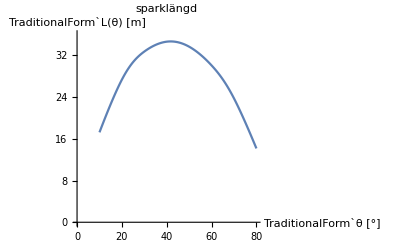

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

```mathematica
ClearAll["`*"]
```

Enter given data.

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Define differential equations and there initial conditions.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Solve the DE.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Example for θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

The curve for different angles.

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

The function for kick length.

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Example

```mathematica
len[45°]
```

A table for different angles.

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Higher accuracy around the max value.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Now, search for the maximum.

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```